```mathematica
$Assumptions=ω>0&&ϵ>0&&Emax>0&&Emax>ϵ&&τ∈Reals&&m>0;
Integrate[1/(p^2+ω^2), {p,-Infinity,Infinity}]
```

π/ω

```mathematica
Integrate[E^(I e τ)/e,{e,Emax,Infinity}]
```

Gamma[0,-ⅈ Emax τ]

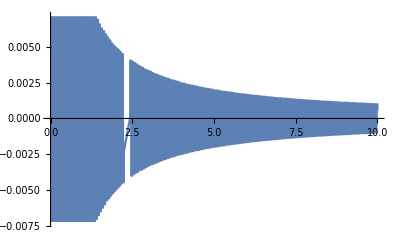

```mathematica
Plot[Im[Gamma[0,-ⅈ  100 τ]],{τ,0,10}]
```

```mathematica
m=1;
Emax=20;
ω[p_]:=Sqrt[p^2+m^2]
NIntegrate[1/(ω[p]ω[q]ω[p+q]ω[k]ω[p+k])1/Ω1 1/Ω2 HeavisideTheta[Ω1-Emax]HeavisideTheta[Ω2-Emax]/.{Ω1-> ω[p]+ω[q]+ω[p+q],Ω2-> ω[p]+ω[k]+ω[p+k]},
{p,-Infinity,Infinity},{q,-Infinity,Infinity},{k,-Infinity,Infinity},
AccuracyGoal->6,Method-> {"GlobalAdaptive","MaxErrorIncreases"->20000 }]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 20000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00180081 and 0.000199541 for the integral and error estimates.

0.00180081

```mathematica
NIntegrate[1/(ω[p1]ω[p2]ω[p3]ω[p1+p2+p3])1/Ω HeavisideTheta[Ω-Emax]/.{Ω-> ω[p1]+ω[p2]+ω[p3]+ω[p1+p2+p3]}
,{p1,-Infinity,Infinity},{p2,-Infinity,Infinity},{p3,-Infinity,Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.38887 and 0.0336127 for the integral and error estimates.

1.38887